Badges indicate graded exercises for certification

Make graphics of 5 concentric circles centered at {0,0} with radii 1, 2, …, 5.

Expected Output »

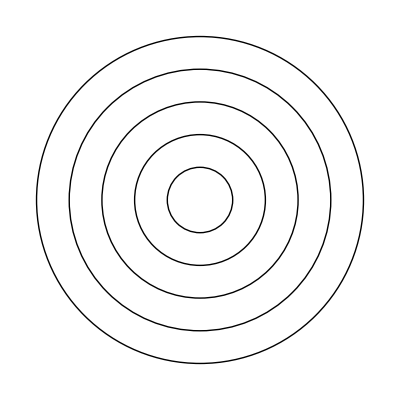

```mathematica
Graphics[Table[Circle[{0, 0}, r], {r, 1, 5}]]
```

-Graphics-

Make 10 concentric circles with random colors.

Expected Output »

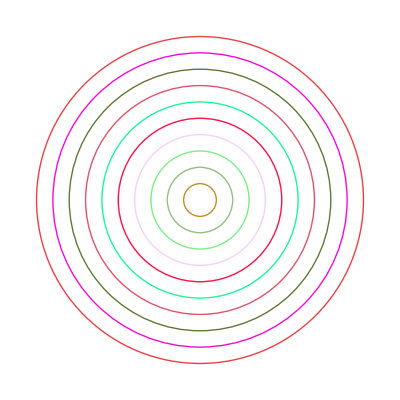

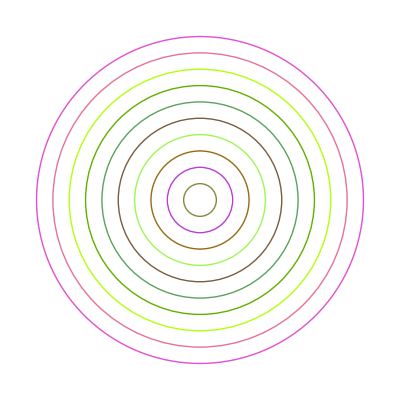

```mathematica
Graphics[Table[{RandomColor[], Circle[{0, 0}, r]}, {r, 1, 10}]]
```

Make graphics of a 10×10 grid of circles with radius 1 centered at integer points {x,y}.

Expected Output »

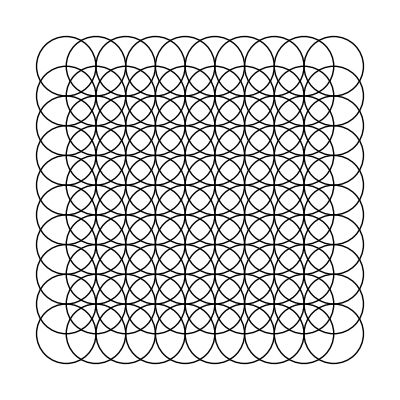

```mathematica
Graphics[Table[Circle[{x, y}, 1], {x, 1, 10}, {y, 1, 10}]]
```

-Graphics-

Make a 10×10 grid of points with coordinates at integer positions up to 10.

Expected Output »

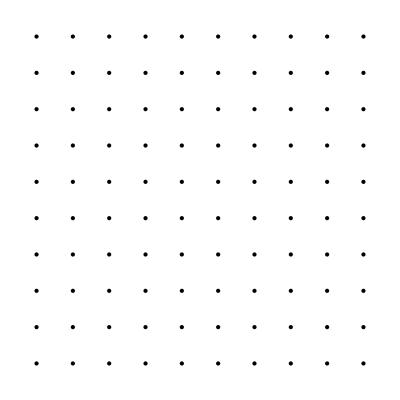

```mathematica
Graphics[Point /@ Tuples[Range[10], 2]]
```

-Graphics-

Make a Manipulate to create an n×n regular grid of points at integer positions, with n going from 5 to 20.

Expected Output »

```mathematica
Manipulate[
 Graphics[Point /@ Tuples[Range[n], 2]],
 {{n, 5, "Grid Size"}, 5, 20, 1, Appearance -> "Labeled"}
]
```

Make a Manipulate with between 1 and 20 concentric circles.

Expected Output »

```mathematica
Manipulate[
 Graphics[Table[Circle[{0, 0}, r], {r, 1, n}]],
 {{n, 1, "Number of Circles"}, 1, 20, 1, Appearance -> "Labeled"}
]
```

Make a graphic of 30 radius-1 circles with random colors at random integer coordinates up to 10.

Expected Output »

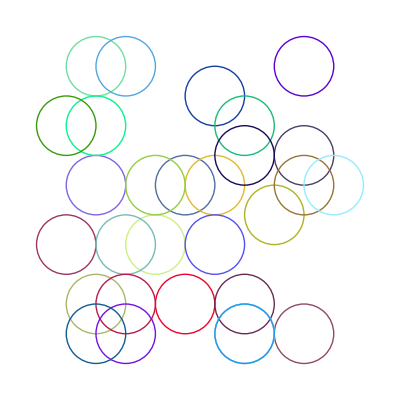

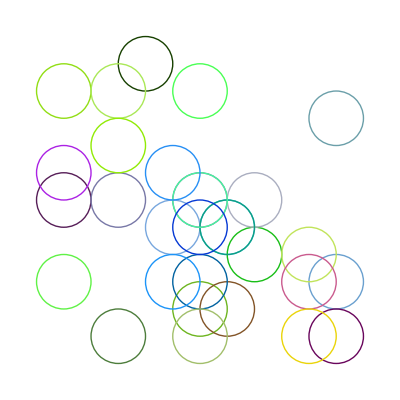

```mathematica
Graphics[Table[{RandomColor[],Circle[RandomInteger[{0, 10}, 2], 1]}, {30}]]
```

Display 100 polygons with radius 10, opacity 0.5, random choices of colors, random number of sides between 3 and 8, and centered at random integer coordinates up to 100.

Expected Output »

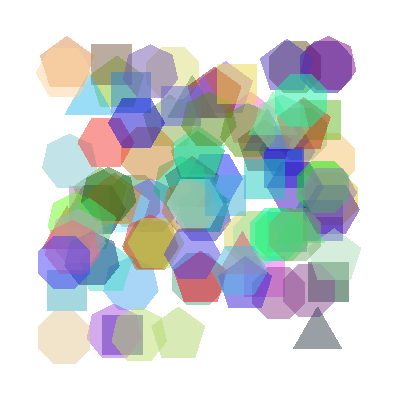

```mathematica
Graphics[Table[{RandomColor[Opacity[0.5]], RegularPolygon[RandomInteger[{3, 8}], {RandomInteger[100], RandomInteger[100]}, 10]}, {100}], ImageSize -> 600]
```

RandomColor::bdmdl: Opacity[0.5] is not a valid model specification. Models can be specified through color directives patterns.

-Graphics-

Place 50 spheres with random colors at random integer coordinates up to 10.

Expected Output »

-Graphics3D-

```mathematica
SeedRandom[123]; (* Define a semente aleatória para reprodução *)

Graphics3D[Table[{RandomColor[], Sphere[{RandomInteger[10], RandomInteger[10], RandomInteger[10]}, 1]}, {50}], 
  Boxed -> False, Axes -> False]
```

-Graphics3D-

Make a 10×10×10 array of spheres with RGB components ranging from 0 to 1. The spheres should be centered at consecutive integer coordinates increasing from (1,1,1), and should just touch each other. The RGB components of each sphere should be in direct proportion to the x, y and z components of that sphere’s center.

Expected Output »

-Graphics3D-

```mathematica
Graphics3D[Table[
  {
    RGBColor[x/10, y/10, z/10], 
    Sphere[{x, y, z}, 0.5]
  },
  {x, 1, 10},
  {y, 1, 10},
  {z, 1, 10}
]]
```

-Graphics3D-

Make a 10×10×10 array of points in 3D, with each point having a random color.

Expected Output »

-Graphics3D-

```mathematica
Graphics3D[Table[
  {RandomColor[], Point[{x, y, z}]},
  {x, 1, 10},
  {y, 1, 10},
  {z, 1, 10}
]]
```

-Graphics3D-

Make a Manipulate with t varying between −2 and +2 that shows 10 circles of radius x centered at {t*x,0} with x going from 1 to 10 in steps of 1.

Expected Output »

```mathematica
Manipulate[
 Graphics[Table[
   {
    Circle[{t * x, 0}, x],
    Text[Style["Radius: " <> ToString[x], Black, Bold], {t * x, x + 0.5}]
   },
   {x, 1, 10}
 ]],
 {{t, 0, "t"}, -2, 2, 0.1, Appearance -> "Labeled"}
]
```

Make a 5×5 array of regular hexagons with size 1/2, centered at integer points.

Expected Output »

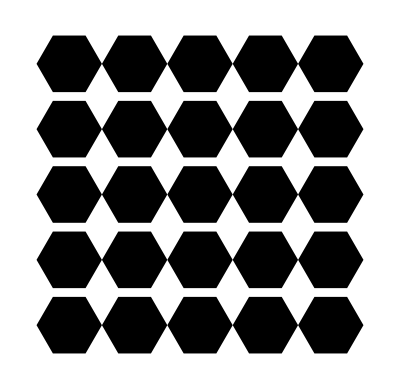

```mathematica
Graphics[Table[
  {
    EdgeForm[Black], 
    RegularPolygon[6, {x, y}, 1/2]
  },
  {x, 1, 5},
  {y, 1, 5}
]]
```

-Graphics-

Make a line in 3D that goes through 50 random points with integer coordinates randomly chosen up to 50.

Expected Output »

-Graphics3D-

```mathematica
Graphics3D[Line[RandomInteger[{0, 50}, {50, 3}]]]
```

-Graphics3D-

Take the first two digits of numbers from 10 to 100 and draw a line that uses them as coordinates.

Expected Output »

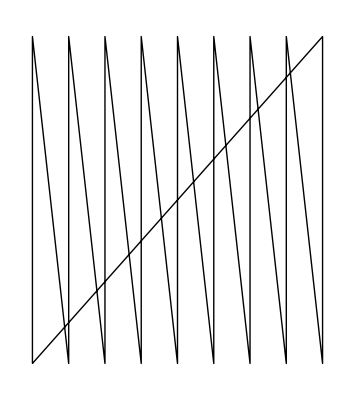

```mathematica
Graphics[Line[Table[IntegerDigits[n][[1 ;; 2]], {n, 10, 100}]]]
```

-Graphics-

Take the first 3 digits of numbers from 100 to 1000 and draw a line in 3D that uses them as coordinates.

Expected Output »

-Graphics3D-

```mathematica
Graphics3D[Line[Table[IntegerDigits[n][[1 ;; 3]], {n, 100, 1000}]]]
```

-Graphics3D-